# Perturbation methods and MoM

## Uniform 1D flow with f=\Xi

#### O(1)

```mathematica
Remove["Global`*"];SetDirectory[NotebookDirectory[]];<<ToMatlab.m
FullSimplify[DSolve[{St*v0'[t]==(U0-v0[t]),y0'[t]==v0[t],v0[0]==V0,y0[0]==Y0},{y0[t],v0[t]},t]]
```

{{v0[t]→U0+ⅇ^(-t/St) (-U0+V0),y0[t]→t U0+(-1+ⅇ^(-t/St)) St (U0-V0)+Y0}}

#### O(epsilon)

```mathematica
Remove["Global`*"];SetDirectory[NotebookDirectory[]];<<ToMatlab.m
v0=U0+ⅇ^(-t/St) (-U0+V0);
y0=t U0+(-1+ⅇ^(-t/St)) St (U0-V0)+Y0;
FullSimplify[DSolve[{St*v1'[t]==(U0-v0)+(0-v1[t]),y1'[t]==v1[t],v1[0]==0,y1[0]==0},{y1[t],v1[t]},t]]
```

{{v1[t]→(ⅇ^(-t/St) t (U0-V0))/St,y1[t]→(St-ⅇ^(-t/St) (St+t)) (U0-V0)}}

#### Second moment

```mathematica
v1=(ⅇ^(-t/St) t (U0-V0))/St;
y1=(St-ⅇ^(-t/St) (St+t)) (U0-V0);
yy=FullSimplify[Xip2*y1^2]
vv=FullSimplify[Xip2*v1^2]
yyy=FullSimplify[Xip3*y1^3]
vvv=FullSimplify[Xip3*v1^3]
yyyy=FullSimplify[Xip4*y1^4]
vvvv=FullSimplify[Xip4*v1^4]
```

(St-ⅇ^(-t/St) (St+t))^2 (U0-V0)^2 Xip2

(ⅇ^(-(2 t)/St) t^2 (U0-V0)^2 Xip2)/St^2

(St-ⅇ^(-t/St) (St+t))^3 (U0-V0)^3 Xip3

(ⅇ^(-(3 t)/St) t^3 (U0-V0)^3 Xip3)/St^3

(St-ⅇ^(-t/St) (St+t))^4 (U0-V0)^4 Xip4

(ⅇ^(-(4 t)/St) t^4 (U0-V0)^4 Xip4)/St^4

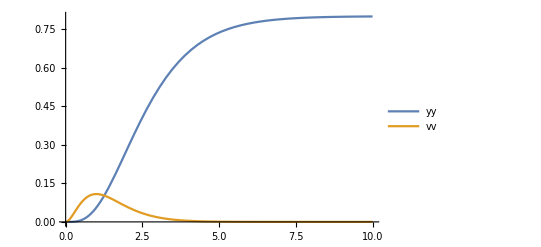

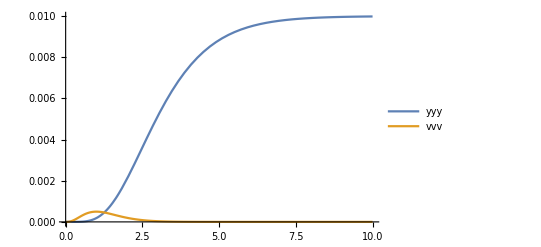

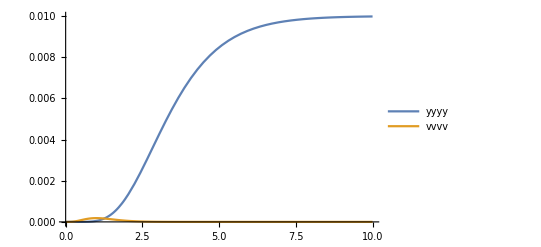

```mathematica
U0=1;
V0=0;
Y0=0;
Xip2=0.8;
Xip3=0.01;
Xip4=0.01;
St=1;
Plot[{yy,vv},{t,0,10},PlotLegends->"Expressions"]
Plot[{yyy,vvv},{t,0,10},PlotLegends->"Expressions"]
Plot[{yyyy,vvvv},{t,0,10},PlotLegends->"Expressions"]
```

## SF 1D flow with f=\Xi

#### O(1)

```mathematica
Remove["Global`*"];SetDirectory[NotebookDirectory[]];<<ToMatlab.m
FullSimplify[DSolve[{St*v0'[t]==(-k*y0[t]-v0[t]),y0'[t]==v0[t],v0[0]==V0,y0[0]==Y0},{y0[t],v0[t]},t]]
```

{{v0[t]→(ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) ((1+√(1-4 k St)+ⅇ^((√(1-4 k St) t)/St) (-1+√(1-4 k St))) V0-2 (-1+ⅇ^((√(1-4 k St) t)/St)) k Y0))/(2 √(1-4 k St)),y0[t]→(ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) (2 (-1+ⅇ^((√(1-4 k St) t)/St)) St V0+(-1+√(1-4 k St)+ⅇ^((√(1-4 k St) t)/St) (1+√(1-4 k St))) Y0))/(2 √(1-4 k St))}}

#### O(epsilon)

```mathematica
Remove["Global`*"];SetDirectory[NotebookDirectory[]];<<ToMatlab.m
v0=(ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) ((1+√(1-4 k St)+ⅇ^((√(1-4 k St) t)/St) (-1+√(1-4 k St))) V0-2 (-1+ⅇ^((√(1-4 k St) t)/St)) k Y0))/(2 √(1-4 k St));
y0=(ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) (2 (-1+ⅇ^((√(1-4 k St) t)/St)) St V0+(-1+√(1-4 k St)+ⅇ^((√(1-4 k St) t)/St) (1+√(1-4 k St))) Y0))/(2 √(1-4 k St));
FullSimplify[DSolve[{St*v1'[t]==(-k*y0-v0)+(-k-v1[t]),y1'[t]==v1[t],v1[0]==0,y1[0]==0},{y1[t],v1[t]},t]]
```

{{v1[t]→1/(2 k St √(1-4 k St))ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) (-2 ⅇ^(((1+√(1-4 k St)) t)/(2 St)) k^2 St √(1-4 k St)+(-1-√(1-4 k St)+k St (3+√(1-4 k St))) V0+k (-1+2 k St-√(1-4 k St)) Y0+ⅇ^((√(1-4 k St) t)/St) (V0-√(1-4 k St) V0+k St (-3+√(1-4 k St)) V0-k (-1+2 k St+√(1-4 k St)) Y0)+2 ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) √(1-4 k St) (V0+k (k St-St V0+Y0))),y1[t]→1/2 (2 k (St-t)-2 St V0+(ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) ((-1+2 k St+√(1-4 k St)) V0+k (-1+√(1-4 k St)) Y0))/(k √(1-4 k St))+(ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) ((1-2 k St+√(1-4 k St)) V0+k (1+√(1-4 k St)) Y0))/(k √(1-4 k St))-(2 ⅇ^(-t/St) (V0+k (k St-St V0+Y0)))/k)}}

#### Second moment

```mathematica
v1=1/(2 k St √(1-4 k St))ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) (-2 ⅇ^(((1+√(1-4 k St)) t)/(2 St)) k^2 St √(1-4 k St)+(-1-√(1-4 k St)+k St (3+√(1-4 k St))) V0+k (-1+2 k St-√(1-4 k St)) Y0+ⅇ^((√(1-4 k St) t)/St) (V0-√(1-4 k St) V0+k St (-3+√(1-4 k St)) V0-k (-1+2 k St+√(1-4 k St)) Y0)+2 ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) √(1-4 k St) (V0+k (k St-St V0+Y0)));
y1=1/2 (2 k (St-t)-2 St V0+(ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) ((-1+2 k St+√(1-4 k St)) V0+k (-1+√(1-4 k St)) Y0))/(k √(1-4 k St))+(ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) ((1-2 k St+√(1-4 k St)) V0+k (1+√(1-4 k St)) Y0))/(k √(1-4 k St))-(2 ⅇ^(-t/St) (V0+k (k St-St V0+Y0)))/k);
yy=Simplify[Xip2*y1^2]
vv=Simplify[Xip2*v1^2]
yyy=Simplify[Xip3*y1^3]
vvv=Simplify[Xip3*v1^3]
yyyy=Simplify[Xip4*y1^4]
vvvv=Simplify[Xip4*v1^4]
```

1/4 Xip2 (2 k (St-t)-2 St V0+(ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) ((-1+2 k St+√(1-4 k St)) V0+k (-1+√(1-4 k St)) Y0))/(k √(1-4 k St))+(ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) ((1-2 k St+√(1-4 k St)) V0+k (1+√(1-4 k St)) Y0))/(k √(1-4 k St))-(2 ⅇ^(-t/St) (V0+k (k St-St V0+Y0)))/k)^2

-1/(4 k^2 St^2 (-1+4 k St))ⅇ^(-((1+√(1-4 k St)) t)/St) Xip2 (2 ⅇ^(((1+√(1-4 k St)) t)/(2 St)) k^2 St √(1-4 k St)+(1+√(1-4 k St)-k St (3+√(1-4 k St))) V0+k (1-2 k St+√(1-4 k St)) Y0+ⅇ^((√(1-4 k St) t)/St) ((-1+√(1-4 k St)-k St (-3+√(1-4 k St))) V0+k (-1+2 k St+√(1-4 k St)) Y0)-2 ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) √(1-4 k St) (k^2 St+V0+k (-St V0+Y0)))^2

1/8 Xip3 (2 k (St-t)-2 St V0+(ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) ((-1+2 k St+√(1-4 k St)) V0+k (-1+√(1-4 k St)) Y0))/(k √(1-4 k St))+(ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) ((1-2 k St+√(1-4 k St)) V0+k (1+√(1-4 k St)) Y0))/(k √(1-4 k St))-(2 ⅇ^(-t/St) (V0+k (k St-St V0+Y0)))/k)^3

-1/(8 k^3 St^3 (1-4 k St)^(3/2))ⅇ^(-(3 (1+√(1-4 k St)) t)/(2 St)) Xip3 (2 ⅇ^(((1+√(1-4 k St)) t)/(2 St)) k^2 St √(1-4 k St)+(1+√(1-4 k St)-k St (3+√(1-4 k St))) V0+k (1-2 k St+√(1-4 k St)) Y0+ⅇ^((√(1-4 k St) t)/St) ((-1+√(1-4 k St)-k St (-3+√(1-4 k St))) V0+k (-1+2 k St+√(1-4 k St)) Y0)-2 ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) √(1-4 k St) (k^2 St+V0+k (-St V0+Y0)))^3

1/16 Xip4 (2 k (St-t)-2 St V0+(ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) ((-1+2 k St+√(1-4 k St)) V0+k (-1+√(1-4 k St)) Y0))/(k √(1-4 k St))+(ⅇ^(-((1+√(1-4 k St)) t)/(2 St)) ((1-2 k St+√(1-4 k St)) V0+k (1+√(1-4 k St)) Y0))/(k √(1-4 k St))-(2 ⅇ^(-t/St) (V0+k (k St-St V0+Y0)))/k)^4

1/(16 k^4 St^4 (1-4 k St)^2)ⅇ^(-(2 (1+√(1-4 k St)) t)/St) Xip4 (2 ⅇ^(((1+√(1-4 k St)) t)/(2 St)) k^2 St √(1-4 k St)+(1+√(1-4 k St)-k St (3+√(1-4 k St))) V0+k (1-2 k St+√(1-4 k St)) Y0+ⅇ^((√(1-4 k St) t)/St) ((-1+√(1-4 k St)-k St (-3+√(1-4 k St))) V0+k (-1+2 k St+√(1-4 k St)) Y0)-2 ⅇ^(((-1+√(1-4 k St)) t)/(2 St)) √(1-4 k St) (k^2 St+V0+k (-St V0+Y0)))^4

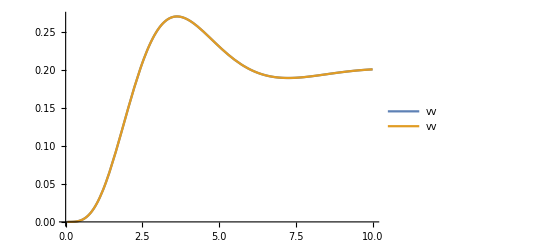

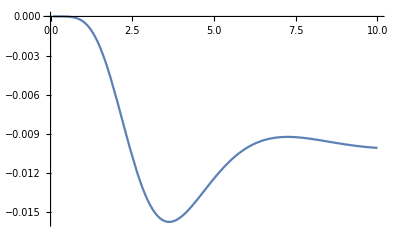

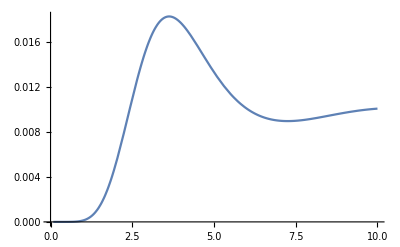

```mathematica
k=1;
V0=0;
Y0=-1;
Xip2=0.2;
Xip3=0.01;
Xip4=0.01;
St=1;
Plot[{vv,vv},{t,0,10},PlotLegends->"Expressions"]
Plot[{vvv},{t,0,10},PlotLegends->"Expressions"]
Plot[{vvvv},{t,0,10},PlotLegends->"Expressions"]
```

## Probando varios coeffs

```mathematica
Remove["Global`*"];SetDirectory[NotebookDirectory[]];<<ToMatlab.m
FullSimplify[DSolve[{y''[t]-(1+a1)/St*y'[t]==1/St*(1+a1)*U0,y[0]==Y0,y'[0]==V0},{y[t]},t]]
FullSimplify[DSolve[{y''[t]-(1)/St*y'[t]==1/St*(1)*U0,y[0]==Y0,y'[0]==V0},{y[t]},t]]
FullSimplify[DSolve[{y''[t]-(a1)/St*y'[t]==1/St*(a1)*U0,y[0]==0,y'[0]==0},{y[t]},t]]
FullSimplify[-t U0+(-1+ⅇ^(t/St)) St (U0+V0)+Y0+-((St-ⅇ^((a1 t)/St) St+a1 t) U0)/a1]
```

{{y[t]→-t U0+((-1+ⅇ^(((1+a1) t)/St)) St (U0+V0))/(1+a1)+Y0}}

{{y[t]→-t U0+(-1+ⅇ^(t/St)) St (U0+V0)+Y0}}

{{y[t]→-((St-ⅇ^((a1 t)/St) St+a1 t) U0)/a1}}

-t U0-((St-ⅇ^((a1 t)/St) St+a1 t) U0)/a1+(-1+ⅇ^(t/St)) St (U0+V0)+Y0

```mathematica
Remove["Global`*"];SetDirectory[NotebookDirectory[]];<<ToMatlab.m
Simplify[DSolve[{St*v'[t]==(1+a1+a2)*(U0-v[t]),y'[t]==v[t],y[0]==Y0,v[0]==V0},{y[t],v[t]},t]]
v=ⅇ^(-((1+a1+a2) t)/St) ((-1+ⅇ^(((1+a1+a2) t)/St)) U0+V0);
y=t U0-(ⅇ^(-((1+a1+a2) t)/St) (-1+ⅇ^(((1+a1+a2) t)/St)) St (U0-V0))/(1+a1+a2)+Y0;
```

{{v[t]→ⅇ^(-((1+a1+a2) t)/St) ((-1+ⅇ^(((1+a1+a2) t)/St)) U0+V0),y[t]→t U0-(ⅇ^(-((1+a1+a2) t)/St) (-1+ⅇ^(((1+a1+a2) t)/St)) St (U0-V0))/(1+a1+a2)+Y0}}

```mathematica
Simplify[DSolve[{St*vh'[t]==(1)*(U0-vh[t]),yh'[t]==vh[t],yh[0]==Y0,vh[0]==V0},{yh[t],vh[t]},t]]
Simplify[DSolve[{St*v0'[t]==0,y0'[t]==v0[t],y0[0]==0,v0[0]==0},{y0[t],v0[t]},t]]
```

{{vh[t]→ⅇ^(-t/St) ((-1+ⅇ^(t/St)) U0+V0),yh[t]→t U0-ⅇ^(-t/St) (-1+ⅇ^(t/St)) St (U0-V0)+Y0}}

{{v0[t]→0,y0[t]→0}}

```mathematica
Simplify[DSolve[{St*v1'[t]==(U0-0),y1'[t]==v1[t],y1[0]==0,v1[0]==0},{y1[t],v1[t]},t]]
Simplify[DSolve[{St*v2'[t]==(U0-0)+(0-(t U0)/St),y2'[t]==v2[t],y2[0]==0,v2[0]==0},{y2[t],v2[t]},t]]
```

{{v1[t]→(t U0)/St,y1[t]→(t^2 U0)/(2 St)}}

{{v2[t]→((2 St-t) t U0)/(2 St^2),y2[t]→((3 St-t) t^2 U0)/(6 St^2)}}

```mathematica
vv=Simplify[ⅇ^(-t/St) ((-1+ⅇ^(t/St)) U0+V0)+a1*(t U0)/St+a1^2*((2 St-t) t U0)/(2 St^2)*0]
```

(a1 t U0)/St+ⅇ^(-t/St) ((-1+ⅇ^(t/St)) U0+V0)

```mathematica
Simplify[DSolve[{St*v0'[t]==(1)*(U0-v0[t]),y0'[t]==v0[t],y0[0]==Y0,v0[0]==V0},{y0[t],v0[t]},t]]
Simplify[DSolve[{St*v1'[t]==(U0-ⅇ^(-t/St) ((-1+ⅇ^(t/St)) U0+V0))+(0-v1[t]),y1'[t]==v1[t],y1[0]==0,v1[0]==0},{y1[t],v1[t]},t]]
Simplify[ⅇ^(-t/St) ((-1+ⅇ^(t/St)) U0+V0)+a1*(ⅇ^(-t/St) t (U0-V0))/St]
```

{{v0[t]→ⅇ^(-t/St) ((-1+ⅇ^(t/St)) U0+V0),y0[t]→t U0-ⅇ^(-t/St) (-1+ⅇ^(t/St)) St (U0-V0)+Y0}}

{{v1[t]→(ⅇ^(-t/St) t (U0-V0))/St,y1[t]→ⅇ^(-t/St) ((-1+ⅇ^(t/St)) St-t) (U0-V0)}}

(ⅇ^(-t/St) (a1 t (U0-V0)+St ((-1+ⅇ^(t/St)) U0+V0)))/St

```mathematica
Simplify[Y]
Simplify[Y0+Y1+Y2]
```

-1/(1+st^2)(st+a1 st+a2 st+st^3+a1 st^3+a2 st^3-ⅇ^(t/st) st^3-a1 ⅇ^(t/st) st^3-a2 ⅇ^(t/st) st^3+st v0-ⅇ^(t/st) st v0+st^3 v0-ⅇ^(t/st) st^3 v0-y0-st^2 y0-(1+a1+a2) st Cos[t]+(1+a1+a2) st^2 Sin[t])

-1/(1+st^2)(st+a1 st+a2 st+st^3+a1 st^3+a2 st^3-ⅇ^(t/st) st^3-a1 ⅇ^(t/st) st^3-a2 ⅇ^(t/st) st^3+st v0-ⅇ^(t/st) st v0+st^3 v0-ⅇ^(t/st) st^3 v0-y0-st^2 y0-(1+a1+a2) st Cos[t]+(1+a1+a2) st^2 Sin[t])

```mathematica
Simplify[DSolve[{y''[t]-(1/st)*y'[t]==0*(a2)*Sin[t],y[0]==0,y'[0]==0},y[t],t]]
```

{{y[t]→0}}

### Third moments

```mathematica
Yip=tp*y1+(tpp-tppm)*y2
Yjp=tp*yj1+(tpp-tppm)*yj2
Ykp=tp*yk1+(tpp-tppm)*yk2
Expand[Simplify[Yip*Yjp*Ykp]]
```

tp yi1+(tpp-tppm) yi2

tp yj1+(tpp-tppm) yj2

tp yk1+(tpp-tppm) yk2

```mathematica
Expand[(tp*y1+(tpp-tppm)*y2)^3]
```

```mathematica
tp^3 y1^3-3 tp^2 tppm y1^2 y2-3 tppm^2 y2^3+2 tppm^3 y2^3
```

```mathematica
-3 tppm^2 y1^2 y2-3  tppm^2 y2^3+2 tppm^3 y2^3
```